## parameters definition

```mathematica
stdpar={e->1.60218 10^-19(*unit charge[C]*),kB->1.38066 10^-23(*Boltzmann constant[J/K]*),
h->6.62607 10^-34(*Planck’s constant[Js]*),hbar->h/(2 Pi)(*[Js]*),
e0->8.85418 10^-12(*permittivity in vaccum[F/m]*),m0->9.10938 10^-31(*effective mass of electron in vaccum[kg]*),
eox->3.9 e0(*permittivity of oxide[F/m]*),
esi->11.8 e0(*permittivity of silicon according to SILVACO[F/m]*),T->300(*temperature[K]*)};
```

```mathematica
unipar={um->10^-6,nm->10^-9,uA->10^-6,mA->10^-3,nA->10^-9};
```

```mathematica
devpar={tox->16.11 nm,lch->.5 um};
```

## 2.3 Channel Charge Theory

```mathematica
ChargeNutral=Qg+Qint+Qs==0;
GateBiaS=Vg==Vox+ϕs+ψms/.Vox->Solve[ChargeNutral,Qg][[1,1,2]]/Cox//ExpandAll//TraditionalForm
```

Vg==-Qint/Cox-Qs/Cox+ψms+ϕs

### channel charge theory

```mathematica
n=np0 Exp[q V/(kB T)];p=pp0 Exp[-q V/(kB T)];F1=Integrate[F,{F,0,F}];F2=Integrate[q/ϵs ((n-np0)-(p-pp0)),{V,0,V}];
eqQs=Solve[F1==F2,F][[2,1,2]] ϵs
```

√2 √(-kB np0 T+ⅇ^((q V)/(kB T)) kB np0 T-kB pp0 T+ⅇ^(-(q V)/(kB T)) kB pp0 T-np0 q V+pp0 q V) √ϵs

```mathematica
Module[{},]
```

## 2.3.2 Depletion

An N-type MOSFET in which NA>>ND, can be simplified into d^2/dx^2 ϕ==q/ϵ_Si N_A, assuming that the width of depletion layer in the semiconductor is X_dep, which can expressed as follows:

```mathematica
Potential01=DSolve[{ϕ''[x]==q/EPSSi NA,ϕ[0]==ϕs,ϕ'[0]==-Es},ϕ[x],x][[1,1,2]]//FullSimplify;
Potential02=DSolve[{ϕ''[x]==q/EPSSi NA,ϕ'[Xdep]==0,ϕ[Xdep]==0},ϕ[x],x][[1,1,2]]//FullSimplify;
ϕs/.ϕs->Potential02/.x->0;
Potential02/ϕs//Apart//Together//Factor;
Xdep/.Xdep->Solve[ϕs==Potential02/.x->0,Xdep][[2,1,2]]//TraditionalForm
```

(√2 √EPSSi √ϕs)/(√NA √q)

The depletion charge can be obtained by

```mathematica
Qdep/.Qdep->-q NA Xdep/.Xdep->Solve[ϕs==Potential02/.x->0,Xdep][[2,1,2]]//TraditionalForm
```

-√2 √EPSSi √NA √q √ϕs

```mathematica
Es[ϕs_]:=Sqrt[(2 q Na)/ϵsi] ((vt Exp[-ϕs/vt])+ϕs-vt+Exp[(-2 ϕb/vt)](vt Exp[ϕs/vt])-ϕs-vt)^0.5
```

## depletion regrion

```mathematica
Clear[Ef,sol1,sol2,phi];
Ef[x_]=DSolve[Ef'[x]==-e Na/(ks e0),Ef[x],x][[1,1,2]];sol1=Ef[W]==0;Ef[x]/.C[1]->Solve[sol,C[1]][[1,1,2]]//Factor//TraditionalForm
phi[x_]=DSolve[phi'[x]==-Ef[x]/.C[1]->Solve[sol,C[1]][[1,1,2]],phi[x],x][[1,1,2]]//Simplify;
sol2=phi[W]==0;PHI[x_]=phi[x]/.C[1]->Solve[sol2,C[1]][[1,1,2]];w=Solve[PHI[0]==phiSurf,W][[2,1,2]]//Factor//TraditionalForm
```

Solve::naqs: sol is not a quantified system of equations and inequalities.

Part::partd: Part specification Solve[sol,1]⟦1,1,2⟧ is longer than depth of object.

-(e Na x-e0 ks Solve[sol,1]⟦1,1,2⟧)/(e0 ks)

Solve::naqs: sol is not a quantified system of equations and inequalities.

Part::partd: Part specification Solve[sol,1]⟦1,1,2⟧ is longer than depth of object.

Solve::naqs: sol is not a quantified system of equations and inequalities.

Part::partd: Part specification Solve[sol,1]⟦1,1,2⟧ is longer than depth of object.

Solve::naqs: sol is not a quantified system of equations and inequalities.

General::stop: Further output of Solve::naqs will be suppressed during this calculation.

Part::partd: Part specification Solve[sol,1]⟦1,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Part::partw: Part 2 of {} does not exist.

{}⟦2,1,2⟧

## Electrostatics

```mathematica
Clear["Global`*"]
n[x_]=ni Exp[(EF-Ei[x])/(kB T)]/.{ni->Sqrt[Nc Na Exp[-Eg/(2 kB T)]],Nc->,Na->,Eg->}
p[x_]=ni Exp[(Ei[x]-EF)/(kB T)]
```

```mathematica
phi[x_]=1/e (Ei[xBulk]-Ei[x])
phi[xSurf]
phiF=1/e (Ei[xBulk]-EF)
```

(-Ei[x]+Ei[xBulk])/e

(Ei[xBulk]-Ei[xSurf])/e

(-EF+Ei[xBulk])/e

## Self-Heating Effect

### Temperature in Channel

```mathematica
(*TempOperation=300;*)
Clear["Global`*"]
(*Clear[TempChannel,TempOperation]*)
TempChannel[TempOperation_,Ids_,Vds_]=TempOperation+Rth Ids Vds/.Rth->Rth0/(Wth0+Weff)/.{Rth0->3 10^-2,Wth0->1 10^-6,Weff->0};
TempChannel[300,500 10^-6,5]
TempChannel[30,1000 10^-6,5]
```

375

180

## Band Gap Reference

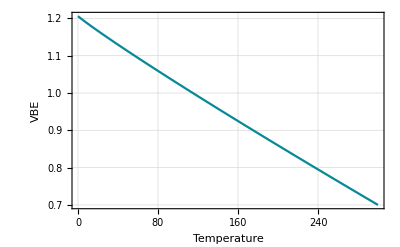

```mathematica
VEB[T_]=VGT0+T/T0 (VEBT0-VGT0)-(η-m) (kB T)/e Log[T/T0]/.VGT0->1.206/.T0->300/.VEBT0->0.7/.η->1/.m->2.3/.kB/e->0.00008633333333333334;
Plot[VEB[T],{T,0,300},Frame->True,GridLines->Automatic,AxesLabel->{"Temperature","VBE"}]
```

## Capacitance model

```mathematica
qg=Solve[Qg+Qinv+Qb==0,Qg][[1,1,2]](*5.2.4*)
```

-Qb-Qinv

```mathematica
lhs=Integrate[ids,{y,0,l}];
rhs=Integrate[-w μ cox (vgs-vth-V),{V,0,vgs-vgd}]//Simplify;
Solve[lhs==rhs,ids][[1,1,2]]//Factor(*5.2.7*)
```

(cox (vgd-vgs) (vgd+vgs-2 vth) w μ)/(2 l)

```mathematica
qinv=-cox (vgs-vth-V);(*5.2.5*)
qqinv=Integrate[w^2 qinv^2 μ/ids,{V,0,vgs-vgd}]/.ids->cox/(2 l) w μ (vgd-vgs) (vgd+vgs-2 vth)//Collect[#,{vgs-vth,vgd-vth},Together]&;
qqg=-qqinv-qb(*5.2.10*)
```

-qb+(2 cox l (vgd-vth)^3 w)/(3 (vgd-vgs) (vgd+vgs-2 vth))-(2 cox l (vgs-vth)^3 w)/(3 (vgd-vgs) (vgd+vgs-2 vth))

```mathematica
cgs=D[qqg,vgs]//Collect[#,(vgs-vth)^2]&//Factor(*5.2.12a*)
cgd=D[qqg,vgd]//Collect[#,vgs-vth]&//Factor(*5.2.12b*)
cgb=D[qqg,vgb](*5.2.12c*)
```

(2 cox l (2 vgd+vgs-3 vth) (vgs-vth) w)/(3 (vgd+vgs-2 vth)^2)

(2 cox l (vgd+2 vgs-3 vth) (vgd-vth) w)/(3 (vgd+vgs-2 vth)^2)

0

```mathematica
$Post=N[#,50]&;
Sin[1]
$Post=.
```

0.84147098480789650665250232163029899962256306079837

```mathematica
qqqg=-qqinv-qb/.vgd->vgs-vds/.vds->vgs-vth(*5.2.13*)
D[qqqg,vgs](*5.2.14a*)
D[qqqg,vgd](*5.2.14b*)
D[qqqg,vgb](*5.2.14c*)
```

-qb+2/3 cox l (vgs-vth) w

(2 cox l w)/3

0

0

```mathematica
sol=ϕ1/.ϕ1->DSolve[{ϕ''[x]==q/ϵsi Na},ϕ[x],x][[1,1,2]]
D[sol,x]
ϕ1==sol/.x->0
Es==D[sol,x]/.x->0
sol1ϕ1/.ϕ1->DSolve[{ϕ''[x]==q/ϵsi Na},ϕ[x],x][[1,1,2]]/.
ϕ2/.ϕ2->DSolve[{ϕ''[x]==q/ϵsi Na,ϕ[xdep]==0,ϕ'[xdep]==0},ϕ[x],x][[1,1,2]]//Collect[#,x]&//Simplify
```

(Na q x^2)/(2 ϵsi)+C[1]+x C[2]

(Na q x)/ϵsi+C[2]

ϕ1==C[1]

Es==C[2]

(Na q (x-xdep)^2)/(2 ϵsi)

## Simplified drain current calculation

physical parameters

```mathematica
nm=10^-9;(*nanometer*)
um=10^-6;(*micrometer*)
NVTO=0.7;(*threshold voltage when VSB is 0, unit: V*)
NGAMMA=0.45;(*substrate bias effect coefficient, unit: V^(1/2)*)
NPHI=0.9;(*potential difference, unit: V*)
TOX=9 nm;(*oxide thickness, unit: m*)
NSUB=9 10^14;(*substrate impurity concentration, unit: cm^-3*)
NUO=350 10^-4;(*channel mobility, unit: m^2/Vs*)
NLAMBDA=0.1;(*channel length modulation coefficient, unit: V^-1*)
nm=10^-9;(*nanometer*)
um=10^-6;(*micrometer*)
PVTO=-0.8;(*threshold voltage when VSB is 0, unit: V*)
PGAMMA=0.4;(*substrate bias effect coefficient, unit: V^(1/2)*)
PPHI=0.8;(*potential difference, unit: V*)
TOX=9 nm;(*oxide thickness, unit: m*)
PSUB=5 10^14;(*substrate impurity concentration, unit: cm^-3*)
PUO=100 10^-4;(*channel mobility, unit: m^2/Vs*)
PLAMBDA=0.2;(*channel length modulation coefficient, unit: V^-1*)
COX=3.9 10^-3;(*capacitance, unit: F/m^2*)
```

NMOS model

triode region 
ⅈ_DS=β (V_DS V_EFF-(V_DS V_DS)/2);

```mathematica
NIDT[VG_,VD_,VS_,W_,L_,VB_]:=NBETA (NVEFF (VD-VS)-((VD-VS) (VD-VS))/2)/.NBETA->(COX NUO W)/L/.NVEFF->VG-VS-NVTH/.NVTH->NGAMMA (√Abs[NPHI+VS-VB]-√NPHI)+NVTO
```

saturation region
ⅈ_DS=1/2 β ⅈ_DS or V_EFF^2=1/2 β V_EFF^2 (λ V_DS+1);

```mathematica
NIDS[VG_,VD_,VS_,W_,L_,VB_]:=0.5 NBETA (NVEFF*NVEFF) (*(1+LAMBDA (VD-VS))*)/.NBETA->NUO COX W/L/.NVEFF->VG-VS-NVTH/.NVTH->NVTO+NGAMMA (Sqrt[Abs[NPHI+VS-VB]]-Sqrt[NPHI])
NIds[VG_,VD_,VS_,W_,L_,VB_]:=NIDT[VG,VD,VS,W,L,VB]/;VG-NVTO-NGAMMA (Sqrt[Abs[NPHI+VS-VB]]-Sqrt[NPHI])≥VD
NIds[VG_,VD_,VS_,W_,L_,VB_]:=NIDS[VG,VD,VS,W,L,VB]/;VG-NVTO-NGAMMA (Sqrt[Abs[NPHI+VS-VB]]-Sqrt[NPHI])<VD
(*NIds[VGS_,VDS_,W_,L_,VSB_]:=0/;VGS-NVTO-NGAMMA (Sqrt[Abs[NPHI+VSB]]-Sqrt[NPHI])<0*)
```

small signal model

```mathematica
Nη[VS_,VB_]:=NGAMMA/(2 Sqrt[NPHI+VS-VB])
Nr0[VG_,VD_,VS_,W_,L_,VB_]:=1/(NLAMBDA NIDS[VG,VD,VS,W,L,VB])
```

##### PMOS model

#### device parameters

#### current charateristics

triode region

```mathematica
Subscript[ⅈ, DS]=β (Subscript[V, DS] Subscript[V, EFF]-(Subscript[V, DS] Subscript[V, DS])/2) ;
```

```mathematica
PIDT[VG_,VD_,VS_,W_,L_,VB_]:=PBETA (PVEFF*(VD-VS)-(1/2)*(VD-VS) (VD-VS))/.PBETA->PUO COX W/L/.PVEFF->VG-VS-PVTH/.PVTH->PVTO+PGAMMA (Sqrt[Abs[PPHI+VS-VB]]-Sqrt[PPHI])
```

saturation region

```mathematica
Subscript[ⅈ, DS]=1/2 β Subscript[ⅈ, DS] or Subscript[V, EFF]^2=1/2 β Subscript[V, EFF]^2 (λ Subscript[V, DS]+1);
```

Set::write: 1/2 or β V_EFF^2 (β (-V_DS^2/2+V_DS V_EFF)) 中的标签 Times 被保护.

```mathematica
PIDS[VG_,VD_,VS_,W_,L_,VB_]:=0.5 PBETA (PVEFF*PVEFF)/.PBETA->PUO COX W/L/.PVEFF->VG-VS-PVTH/.PVTH->PVTO+PGAMMA (Sqrt[Abs[PPHI+VS-VB]]-Sqrt[PPHI])
```

```mathematica
PIds[VG_,VD_,VS_,W_,L_,VB_]:=PIDT[VG,VD,VS,W,L,VB]/;VG-PVTO-PGAMMA (Sqrt[Abs[PPHI+VS-VB]]-Sqrt[PPHI])>=VD
PIds[VG_,VD_,VS_,W_,L_,VB_]:=PIDS[VG,VD,VS,W,L,VB]/;VG-PVTO-PGAMMA (Sqrt[Abs[PPHI+VS-VB]]-Sqrt[PPHI])<VD
```

small signal model

```mathematica
Pη[VS_,VB_]:=PGAMMA/(2 Sqrt[PPHI+VS-VB])
Pr0[VG_,VD_,VS_,W_,L_,VB_]:=1/(PLAMBDA PIDS[VG,VD,VS,W,L,VB])
```

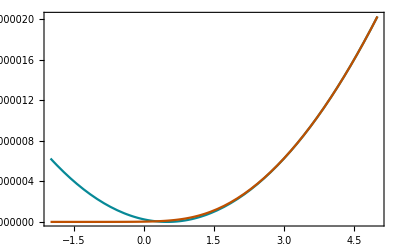

```mathematica
ids=mu cox w/l (vgs-vth)^2;
fitids=mu cox w/l (a Log[1+Exp[1/a (vgs-vth)]])^2;
Plot[Evaluate[{ids,fitids}/.{w->1 10^-6,mu->1000,cox->1 10^-10,l->1 10^-6,vth->0.5,vds->5,a->.5}],{vgs,-2,5},Frame->True]
```